```mathematica
ClearAll["Global`*"]
```

```mathematica
σ[r_]:=1
κ=1;
```

```mathematica
Rmin=1;
Rmax=2;
zRmin=0;
zRmax=1/10;
zpRmin=1/10;
zpRmax=2/10;
```

```mathematica
(*solve with mathematica*)
```

```mathematica
sol=NDSolve[{3 (3 κ-4 r^2 σ[r]) z'[r]^5+(5 κ-8 r^2 σ[r]) z'[r]^7+(κ-2 r^2 σ[r]) z'[r]^9+r (κ-2 r^2 σ[r]) z'[r]^6 z''[r]+2 r^2 z'[r]^4 (-3 r σ[r] z''[r]+2 κ Derivative[3][z][r]+r κ Derivative[4][z][r])+r (-2 (κ+r^2 σ[r]) z''[r]-5 r^2 κ z''[r]^3+2 r κ (2 Derivative[3][z][r]+r Derivative[4][z][r]))+r z'[r]^2 (-3 (κ+2 r^2 σ[r]) z''[r]+30 r^2 κ z''[r]^3+4 r κ (2 Derivative[3][z][r]+r Derivative[4][z][r]))==z'[r] (-κ (2+7 z'[r]^2)+r^2 (σ[r] (2+8 z'[r]^2)+5 κ (1+z'[r]^2) z''[r] (3 z''[r]+4 r Derivative[3][z][r]))),z[Rmin]==zRmin,z[Rmax]==zRmax,z'[Rmin]==zpRmin,z'[Rmax]==zpRmax},z,{r,Rmin,Rmax}][[1]]
```

{z→InterpolatingFunction[…]}

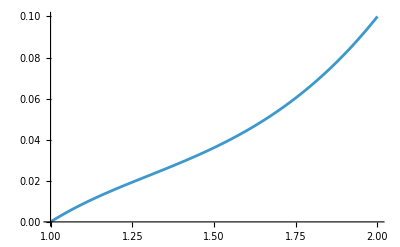

```mathematica
plotmathematica=Plot[z[r]/.sol,{r,Rmin,Rmax}]
```

```mathematica
(*import the solution with python*)
```

```mathematica
tab=Import["/Users/michelecastellana/Documents/finite_elements/solve_ode_with_python/steady_state_no_flow/solution.csv"]
tab=Drop[tab,{1}]
```

```mathematica
tab0=Table[{tab[[i,1]],tab[[i,2]]},{i,1,Length[tab]}]
```

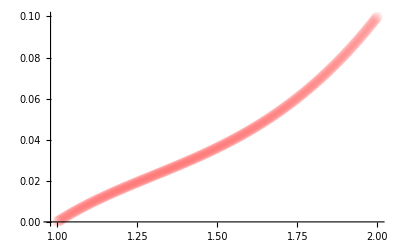

```mathematica
plotpython=ListPlot[tab0,PlotStyle->{Red, Opacity->0.02,PointSize->.02}]
```

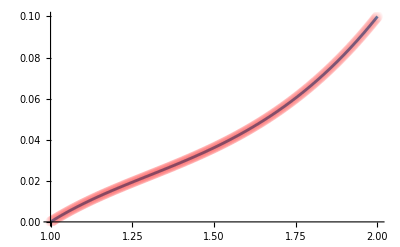

```mathematica
Show[plotmathematica,plotpython]
```